## Load Data

```mathematica
nu=1.4;
data = Import ["/home/marius/MA/CUDA_Simulation_RW/Results/Simulation_06_26/Histogram_origin_peak/histogram_gamma_0.8_nu_0.8_eta_0.8_ta_0.txt","Table"];
tmax =20000;
```

```mathematica
results = Import ["/home/marius/MA/CUDA_Simulation_RW/Results/Simulation_06_26/Histogram_origin_peak/origin_peak_gamma_0.8_nu_1.4_eta_1.4.txt","Table"];
origin = results[[3,All]];
peak = results[[4,All]];
```

## Show Histogram Movie

```mathematica
x= data[[1,All]];
Animate[ 
y=data[[u,All]];
hist = Transpose[{x,y}];
time = tmax/(Length[data]-2)*(u-2);
boundry = {{time^nu,Min[y]},{time^nu,Max[y]}}; 
originPlot = {{0,origin[[u-2]]},{Max[x],origin[[u-2]]}};
peakPlot = {{0,peak[[u-2]]},{Max[x],peak[[u-2]]}};
(* How far could a particle get?*)
ListLogPlot[{hist,boundry},AxesLabel->{"Distance","Relative Number of Particles"}]
,{u,3,Length[data],1}]
```

## Export Histogram Movie

```mathematica
frames = {};

For[u = 2, u ≤Length[data],u++,
y=data[[u,All]];
hist = Transpose[{x,y}];
time = tmax/Length[data]*u;
boundry = {{time^nu,0},{time^nu,Max[y]}};
frame = ListLinePlot[{hist,boundry},AxesLabel->{"Distance","Relative Number of Particles"}];
AppendTo[frames,frame];
(*ListLinePlot[boundry]*)
]
Export["MA/CUDA_Simulation_RW/Results/Histogram_06_18/movie_gamma_0.8_nu_1.3_eta_1.5_ta_0.avi",frames]
```

MA/CUDA_Simulation_RW/Results/Histogram_06_18/movie_gamma_1.3_nu_1.3_eta_1.1_ta_0.avi

## Fit of the PDF :

-4.66178-0.0013994 z

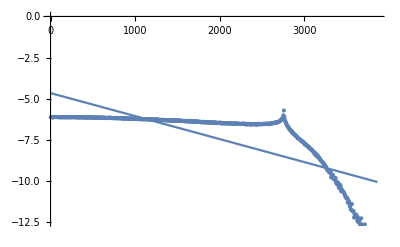

```mathematica
timeStep = 20; (*Between 1 and nTimes*)
nTimes = Length[data]-1;
exp =0.5;
time = tmax/(nTimes-1) * (timeStep-1);
pos= data[[1,All]];
prob=Log[data[[1+timeStep,All]]];
cutOff = Position[prob, _?(# == - Infinity&)][[1,1]]-1;
points = Transpose[{pos[[1;;cutOff]],prob[[1;;cutOff]]}];
fit = Fit[points, {1,z},z]
Show[ 
ListPlot[points],
Plot[fit,{z,pos[[1]],pos[[cutOff]]},AxesLabel->fit]
]
```